Polymerization in a Batch Reactor

```mathematica
zoom={1,2,10,30,60,100};
```

```mathematica
range[func_,max_]:=Quiet@Which[func≤max/zoom[[6]],zoom[[6]],func≤max/zoom[[5]],zoom[[5]],func≤max/zoom[[4]],zoom[[4]],func≤max/zoom[[3]],zoom[[3]],func≤max/zoom[[2]],zoom[[2]],func≤max/zoom[[1]],zoom[[1]]];
```

```mathematica
scale[text_,val_,len_,pos_,off_]:=Text[Framed[Column[{
Style[Row[{text,"-axis scale"}],15],
Row@Flatten@{
ReplacePart[Row@{Framed[Style[Row[{zoom[[#]],"x"}],15],FrameMargins->Small],Spacer[5]}&/@Range@Length@len,
First@First@Position[zoom,val]->
Style[Part[Row@{Framed[Style[Row[{zoom[[#]],"x"}],15],FrameMargins->Small,Background->RGBColor[1,0.705,0.71]],Spacer[5]}&/@Range@Length@len,First@First@Position[zoom,val]],Bold]]}
},Center],FrameMargins->Tiny],Scaled[pos],off];
```

```mathematica
(0.5/zoom)/0.5
```

{1.,0.5,0.1,0.0333333,0.0166667,0.01}

```mathematica
N@100/zoom
```

{100.,50.,10.,3.33333,1.66667,1.}

```mathematica
percent={100,50,10,(*5,*)1}/100;
```

```mathematica
(*L0=1000;*)
Graphics[{
{Thick,Line@{{1,0},{L0,0}}},
Line[{{#,-0.01*L0},{#,0.01*L0}}]&/@Range[0,L0,50],
Text[Style[#*L0,15],{#*L0,-50}]&/@percent
}];
```

```mathematica
Manipulate[
Module[{Mo,kp,t,L0,p,M,f,y,P,ndist1,ndist2,n2,wdist1,wdist2,w2,μn,μw,PD,L1,ymax,xmax},
If[bmth==1,
{Mo=Mo1;kp=kp1;t=t1;L0=1000;
p=1-(Mo*kp*t+1)^-1;(*frac. func. groups reacted*)
M=Mo*(1-p);(*conc. of func. group*)},
{Mo=Mo2;kp=kp2;t=t2;f=0.5;L0=3000;
M=Mo*Exp[√(8*kp^2*f*Io/(ki*kt))*Exp[-ki*t/2]];
p=(kp*M)/(kp*M+kt*term+√(2*kt*ki*f*Io*Exp[-ki*t]));}];

y=(1-p)*p^(#-1)&;(*mole fraction*)
P=y[#]*M&;(*polymer concentration*)

ndist1=Total[y[#]&/@Range[1,L0,0.3]];
ndist2={#,y[#]/ndist1}&/@Range[1,L0,0.3];
n2=Quiet@Interpolation[ndist2];

wdist1=Total[#*y[#]&/@Range[1,L0,0.3]];
wdist2={#,#*y[#]/wdist1}&/@Range[1,L0,0.3];
w2=Quiet@Interpolation[wdist2];

μn=(∑_(j=1)^L0 j*P[j])/(∑_(j=1)^L0 P[j]);(*number avg chain length NACL*)
μw=(∑_(j=1)^L0 j^2*P[j])/(∑_(j=1)^L0 j*P[j]);(*weight avg chain length WACL*)
PD=μw/μn;(*polydispersity*)

L1=x/.Quiet@FindRoot[n2[x]==0.0001,{x,1,1,L0}];
ymax=0.5/range[n2[1],0.5];
xmax=L0/range[L1,L0];

(*Plot[{n2[x],w2[x]},{x,1,xmax},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0,0.6,0]}},
Axes->False,Frame->True,FrameLabel->{Style["monomer units",17],Style["polymer  fraction ",17]},LabelStyle->{14,Black},PlotRange->{0,ymax},PlotRangePadding->{None,{Scaled[0.05],Scaled[0.03]}},ImageSize->{400,450},AspectRatio->1,ImagePadding->{{70,30},{70,50}},PlotRangeClipping->False,
Epilog->{
Inset[Graphics[{
{Thick,Line@{{1,0},{L0,0}}},
Line[{{#,-0.01*L0},{#,0.01*L0}}]&/@Range[0,L0,50],
Text[Style[#*L0,15],{#*L0,-50}]&/@percent
},ImageSize->350],
{xmax/2,-0.004}]
}]*)

(*Graphics[{
Inset@Plot[{n2[x],w2[x]},{x,1,xmax},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0,0.6,0]}},
Axes->False,Frame->True,FrameLabel->{Style["monomer units",17],Style["polymer  fraction ",17]},LabelStyle->{14,Black},PlotRange->{0,ymax},PlotRangePadding->{None,{Scaled[0.05],Scaled[0.03]}},(*ImageSize->{400,400},*)AspectRatio->1,ImagePadding->{{70,10},{40,5}}]
},
ImageSize->{400,450},AspectRatio->1,Frame->{{True,None},{True,None}},FrameLabel->{Style["x-range",16],Style["y-range",16]},LabelStyle->{14,Black},PlotRange->{{1,L0},{0,0.5}}]*)

Plot[{n2[x],w2[x]},{x,1,xmax},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0,0.6,0]}},
Axes->False,Frame->True,FrameLabel->{Style["monomer units",17],Style["polymer  fraction ",17]},LabelStyle->{14,Black},PlotRange->{0,ymax},PlotRangePadding->{None,{Scaled[0.05],Scaled[0.03]}},ImageSize->{400,400},AspectRatio->1,ImagePadding->{{70,10},{90,5}},PlotRangeClipping->False,
Epilog->Inset[Graphics[{
{Thick,Line@{{0,0},{L0,0}}},
Line[{{#,-0.01*L0},{#,0.01*L0}}]&/@Range[0,L0,0.05*L0],
Text[Style[#,12],{#,-0.05*L0}]&/@(percent*L0),
Text[Style["x-range",15],{L0/2,-0.1*L0}],
{AbsoluteThickness[5],Red,Line@{{L1,-0.01*L0},{L1,0.01*L0}}}
},ImageSize->325],
Scaled[{0.5,-0.2}]]
]

],
Control[{{bmth,1,""},{1->" step growth ",2->" free radical "},Setter}],
Delimiter,
Style["initial concentration:",Bold],
PaneSelector[{
1->Control[{{Mo1,0.5,"monomer"},0.5,5,0.1,Appearance->"Labeled",ImageSize->Tiny}],
2->Column[{
Control[{{Mo2,0.5,"monomer"},0.5,5,0.1,Appearance->"Labeled",ImageSize->Tiny}],
Control[{{Io,0.05,"initiator"},0.05,0.5,0.01,Appearance->"Labeled",ImageSize->Tiny}]
}]},Dynamic@bmth],
Delimiter,
Style["rate constant:",Bold],
PaneSelector[{
1->Control[{{kp1,0.1,"reaction"},0.1,1,0.01,Appearance->"Labeled",ImageSize->Tiny}],
2->Column[{
Control[{{kp2,0.5,"reaction"},0.05,1,0.01,Appearance->"Labeled",ImageSize->Tiny}],
Control[{{ki,0.15,"initiation"},0.05,1,0.01,Appearance->"Labeled",ImageSize->Tiny}],
Control[{{kt,0.1,"termination"},0.005,0.1,0.001,Appearance->"Labeled",ImageSize->Tiny}]
}]},Dynamic@bmth],
Delimiter,
PaneSelector[{
1->Control[{{t1,500,"time"},500,5000,1,Appearance->"Labeled",ImageSize->Tiny}],
2->Control[{{t2,0.01,"time"},0.01,50,0.01,Appearance->"Labeled",ImageSize->Tiny}]
},Dynamic@bmth],
Delimiter,
PaneSelector[{2->Column[{
Style["concentration:",Bold],
Control[{{term,0.1,"terminator"},0.005,0.1,0.001,Appearance->"Labeled",ImageSize->Tiny}]
}]},Dynamic@bmth],
ControlPlacement->Left,SaveDefinitions->True]
```

```mathematica
{100,50,10,5,1}/100
```

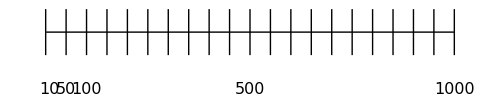

```mathematica
Graphics[{
{Thick,Line@{{1,0},{1000,0}}},
Line[{{#,-10},{#,10}}]&/@Range[0,1000,50],
Text[Style[#,16],{#,-25}]&/@(1000*{100,50,10,5,1}/100)
},ImageSize->500]
```

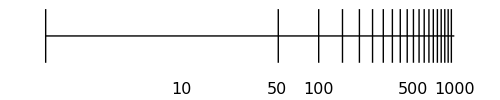

```mathematica
Graphics[{
{Thick,Line[{Log@#1,#2}&@@@{{1,0},{1000,0}}]},
Line[{Log@#1,#2}&@@@{{#,-0.1},{#,0.1}}]&/@Range[1,1000,50],
Text[Style[#,16],{Log@#,-0.2}]&/@(1000*{100,50,10,5,1}/100)
},ImageSize->500]
```

```mathematica
{{1,0},{1000,0}}
{Log@#1,#2}&@@@{{1,0},{1000,0}}
```

{{1,0},{1000,0}}

{{0,0},{Log[1000],0}}

```mathematica
(*Epilog->{
Text[Framed[Style[Subscript["N","S"],Italic,17,Blue],Background->White,FrameStyle->None,FrameMargins->Tiny],{0.15*xmax,n2[0.15*xmax]}],
Text[Framed[Style[Subscript["W","S"],Italic,17,RGBColor[0,0.6,0]],Background->White,FrameStyle->None,FrameMargins->Tiny],{0.85*xmax,w2[0.85*xmax]}],
Text[Style[Column[{
Row[{"polydispersity = ",NumberForm[PD,{4,2}]}],
Row[{"number average ",Style[OverBar@Subscript["N","S"],Italic]," = ",NumberForm[μn,{5,1}]}],
Row[{"weight average ",Style[OverBar@Subscript["W","S"],Italic]," = ",NumberForm[μw,{5,1}]}]
},Alignment->"="],16,Background->White],Scaled[{0.65,0.85}]],
scale["y",range[n2[1],0.5],zoom,{0,1},{-0.5,-1.15}],
scale["x",range[L1,L0],If[bmth==1,{1,1},zoom],{1,0},{0.7,2}]
}*)
```

This Demonstration plots the number fraction N_S (blue) and weight fraction W_S (green) of polymer chains versus the number of monomer units in a polymer chain for step-growth and free-radical polymerization in a batch reactor. Select the type of polymerization with buttons, and use sliders to set reaction rate constants, initial concentrations, and reaction time. The number average chain length OverBar[N_S], the weight average chain length OverBar[W_S] , and the polydispersity are shown. Distributions are calculated using the Flory-Schulz model. Note that the x- and y-axis ranges change as the parameters change, and the red boxes above and below the plot indicate the magnification of that axis range.





The number fraction N_s and weight fraction W_S of polymer chains for a polymer with j monomer units are:

N_S=y_j/(∑y_j),

W_S=(j y_j)/(∑j y_j),

where y_j is mole fraction and p is the fraction of functional groups that have reacted:

y_j=(1-p) p^(j-1).

For step growth polymerization:

p=1-(M_0 k_p t+1)^-1,

M=M_0 (1-p).

For free radical polymerization:

p=k_p M/(k_p M+k_t τ+√(2  k_t k_i f I_0 ⅇ^(-k_i t))),

M=M_0 ⅇ^(√((8 k_p^2 f I_0)/(k_i k_t)) ⅇ^(-k_i t/2)),

where M_0 and I_0 are the initial monomer and initiator concentrations, M is the concentration of a functional group, k_p, k_t, and k_i are the reaction, initiation, and termination rate constants, f is the fraction of polymer chains the initiator initiates, t is time, and τ is the terminator concentration.

The number OverBar[N_S] and weight OverBar[W_S] average chain lengths are:

OverBar[N_S]=(∑j P_j)/(∑P_j),

OverBar[W_S]=(∑j^2 P_j)/(∑j P_j),

where P_j=y_j M is the polymer concentration.

The polydispersity D is:

D=OverBar[W_S]/OverBar[N_S].

Reference:

[1] H. S. Fogler, Elements of Chemical Reaction Engineering, 5th ed., Boston: Pearson Education Inc., 2016.

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

polymerization

Flory-Schulz

polymer chemistry

polydispersity

chemical engineering

average molecular weight

Contributed by: Rachael L. Baumann and Nathan S Nelson

Additional contributions by: John L. Falconer

(University of Colorado Boulder, Department of Chemical and Biological Engineering)